Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{H→Function[{x},(α (1+ProductLog[-ⅇ^(-1+(x β^2)/(α γ))]))/β]}}

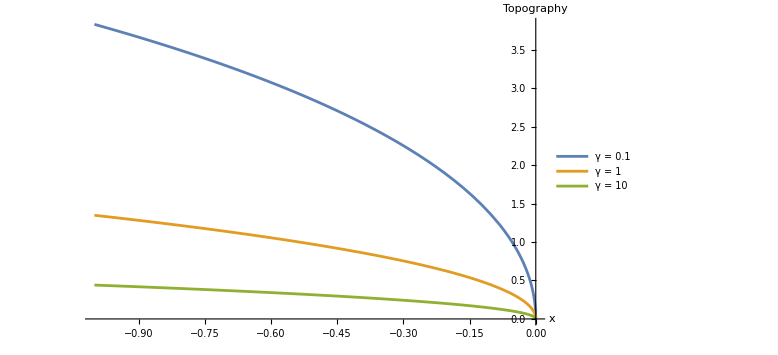

```mathematica
eqn = β* H[x] - γ*H[x]*H'[x] == α;
solLocal = DSolve[{eqn,H[0]==0},H,{x,-1,0}]
Plot[Evaluate[Table[H[x]/. solLocal/. {α->1,β->0.1,γ->a},{a,{0.1,1,10}}]],{x,-1,0},PlotLegends->{"γ = 0.1","γ = 1","γ = 10"},AxesLabel->{"x","Topography"},ImageSize->Large]
```

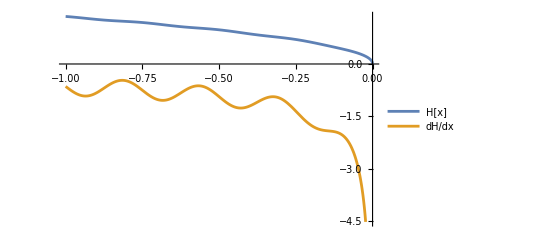

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::nlnum: The function value {ComplexInfinity} is not a list of numbers with dimensions {1} at {x,y[x],y'[x]} = {0.,0.,0.}.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

{}

-Graphics-

```mathematica
(*eqn = η[ H'[x] y'[x]+H[x] y''[x]]-α+β H[x]-γ H[x] H'[x]==0;*)
(*BCs = {y[0]==1,y'[-1]==0};*)
BCs = {y[0]==0};
αval = 1;
βval = 0.1;
γval = 1;
Hval = 0.01*Cos[4*2Pi x] +H[x]/.solLocal[[1]] /.{α->αval,β->βval,γ->γval};
dHdx = D[Hval,x];
Plot[{Hval,dHdx},{x,-1,0},PlotLegends->{"H[x]","dH/dx"}]
(*Hval = x*)
(*eqn = η *D[Hval* y'[x],x]-α+β *Hval-γ *Hval *dHdx==0;*)
eqn = η [Hval* y'[x]+dHdx*y[x]]-α+β *Hval-γ *Hval *dHdx==0;
numSolV = NDSolve[{eqn/. {α->αval,β->βval,γ->γval,η->1},BCs},y[x],{x,-1,0}]
Plot[Evaluate[y[x]/. numSolV],{x,-1,0}]
```